29/12/2020 Mathematica Ising Model

This program is a two-dimensional implementation of the ising model using Monte-Carlo algorithms. The two algorithms used are the Metropolis and Wolff algorithms. The convention used is that 1 denotes spin up (orange) and -1 denotes spin down (blue). [DEFINE K]

Initializing the variables to be used:

```mathematica
J=1;
mu=1;
h=0;
k=1;
T=2;
```

First of all, we'll define a series of function to make a board and simple manipulations of that board.

```mathematica
makeBoard[n_]:=2*RandomInteger[{0,1},{n,n}]-1
sizeBoard[board_]:=Dimensions[board][[1]]
displayBoard[board_]:=MatrixPlot[board,Frame-> False]

getSpin[board_,position_]:=
board[[position[[1]],position[[2]]]]
flipSpin[board_,position_]:=
ReplacePart[board,position->-getSpin[board,position]]
```

Now, we define the functions for the physics calculations

```mathematica
bondEnergy[board_,position_,J_]:=Block[{i,j,n,u},
{i,j}=position;
n=sizeBoard[board];
u=-J*getSpin[board,position]*(getSpin[board,{Mod[(i+1)-1,n]+1,j}]+getSpin[board,{Mod[(i-1)-1,n]+1,j}]+getSpin[board,{i,Mod[(j+1)-1,n]+1}]+getSpin[board,{i,Mod[(j-1)-1,n]+1}])
]

fieldEnergy[board_,position_,h_,mu_]:=
-getSpin[board,position]*mu*h

energy[board_,position_,J_,h_,mu_]:=
bondEnergy[board,position,J]+fieldEnergy[board,position,h,mu]

energyDifference[board_,position_,J_,h_,mu_]:=
-2*energy[board,position,J,h,mu]

boltzmann[de_,T_]:=
Exp[-de/(k*T)]
```

The update functions for the Metropolis and Wolff algorithms are below

```mathematica
updateMetropolis[board_,J_,h_,mu_,T_]:=Block[{n,position,de},
n=sizeBoard[board];
position = RandomInteger[{1,n},2];
de=energyDifference[board,position,J,h,mu];
If[de≤ 0,flipSpin[board,position],If[RandomReal[{0,1}]<boltzmann[de,T],flipSpin[board,position],board]
]
]

nMetropolisUpdates[board_,J_,h_,mu_,T_,n_]:=
Nest[updateMetropolis[#,J,h,mu,T]&,board,n]
```

{{1,-1,-1,-1,1,1,-1,-1,-1,-1},{1,1,-1,1,-1,1,1,1,1,-1},{1,1,1,-1,1,-1,-1,1,-1,-1},{-1,1,-1,-1,1,-1,-1,-1,-1,1},{1,-1,1,-1,-1,1,-1,-1,1,-1},{-1,-1,1,1,1,1,-1,1,1,1},{-1,-1,1,-1,1,-1,-1,1,-1,-1},{-1,-1,-1,1,-1,1,-1,1,1,-1},{1,-1,-1,-1,1,1,1,1,-1,1},{1,-1,-1,1,1,-1,-1,1,1,-1}}

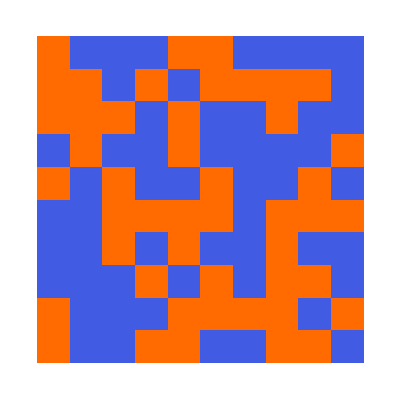

1

{{1,-1,-1,-1,1,1,-1,-1,-1,-1},{1,1,-1,1,-1,1,1,1,1,-1},{1,1,-1,-1,1,-1,-1,1,-1,-1},{-1,1,-1,-1,1,-1,-1,-1,-1,1},{1,-1,1,-1,-1,1,-1,-1,1,-1},{-1,-1,1,1,1,1,-1,1,1,1},{-1,-1,1,-1,1,-1,-1,1,-1,-1},{-1,-1,-1,1,-1,1,-1,1,1,-1},{1,-1,-1,-1,1,1,1,1,-1,1},{1,-1,-1,1,1,-1,-1,1,1,-1}}

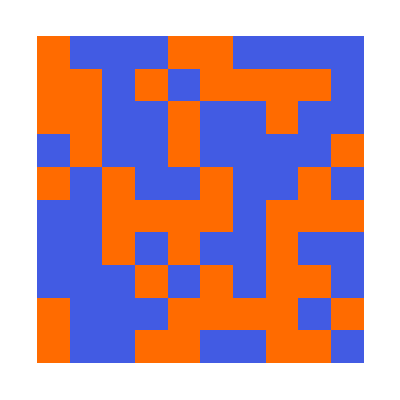

0.717427

```mathematica
board2=makeBoard[10]
displayBoard[board2]
getSpin[board2,{3,3}]
board2=flipSpin[board2,{3,3}]
displayBoard[board2]
```

-Graphics-

10

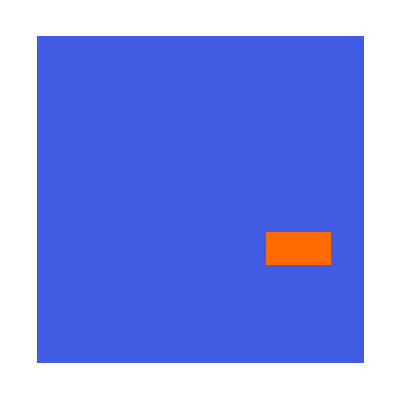

```mathematica
displayBoard[board2]
sizeBoard[board2]
displayBoard[nMetropolisUpdates[board2,J,h,mu,T,20000]]
Animate[displayBoard[nMetropolisUpdates[board2,J,h,mu,T,n]],{n,1,2000,1}]
```